```mathematica
arr = {{"USA-road-d.NY.gr",264346,733846,227,43772974,65595724,56135684,66504768,69225142,75450949,82953021},{"USA-road-d.COL.gr",435666,1057066,138,71897250,103218350,88102700,107326975,113312571,118864055,134476813},{"USA-road-d.FLA.gr",1070376,2712798,57,168026817,246080875,210937815,257773664,268575917,286306652,323138578},{"USA-road-d.CAL.gr",1890815,4657742,32,368398693,534146518,457065109,535693553,568315590,608210621,690760975},{"USA-road-d.E.gr",3598623,8778114,17,911953511,1316539605,1139754311,1284193782,1345675041,1442650047,1650487329},{"USA-road-d.W.gr",6262104,15248146,10,1755942710,2573694280,2135410260,2420192600,2655490590,2836398360,3243565200},{"USA-road-d.CTR.gr",14081816,34292496,5,10914507840,14826297060,12284172700,12143506760,12603239300,13378356680,14593069020},{"USA-road-d.USA.gr",23947347,58333344,3,9879156733,13887132133,12274696566,12697125266,13585971100,14552861733,16468550600}
};
```

```mathematica
list = Array[{arr[[#1,2]],arr[[#1,#2+4]]}&,{Length[arr],7}]
```

{{{264346,43772974},{264346,65595724},{264346,56135684},{264346,66504768},{264346,69225142},{264346,75450949},{264346,82953021}},{{435666,71897250},{435666,103218350},{435666,88102700},{435666,107326975},{435666,113312571},{435666,118864055},{435666,134476813}},{{1070376,168026817},{1070376,246080875},{1070376,210937815},{1070376,257773664},{1070376,268575917},{1070376,286306652},{1070376,323138578}},{{1890815,368398693},{1890815,534146518},{1890815,457065109},{1890815,535693553},{1890815,568315590},{1890815,608210621},{1890815,690760975}},{{3598623,911953511},{3598623,1316539605},{3598623,1139754311},{3598623,1284193782},{3598623,1345675041},{3598623,1442650047},{3598623,1650487329}},{{6262104,1755942710},{6262104,2573694280},{6262104,2135410260},{6262104,2420192600},{6262104,2655490590},{6262104,2836398360},{6262104,3243565200}},{{14081816,10914507840},{14081816,14826297060},{14081816,12284172700},{14081816,12143506760},{14081816,12603239300},{14081816,13378356680},{14081816,14593069020}},{{23947347,9879156733},{23947347,13887132133},{23947347,12274696566},{23947347,12697125266},{23947347,13585971100},{23947347,14552861733},{23947347,16468550600}}}

```mathematica
mat = Transpose[list]
```

{{{264346,43772974},{435666,71897250},{1070376,168026817},{1890815,368398693},{3598623,911953511},{6262104,1755942710},{14081816,10914507840},{23947347,9879156733}},{{264346,65595724},{435666,103218350},{1070376,246080875},{1890815,534146518},{3598623,1316539605},{6262104,2573694280},{14081816,14826297060},{23947347,13887132133}},{{264346,56135684},{435666,88102700},{1070376,210937815},{1890815,457065109},{3598623,1139754311},{6262104,2135410260},{14081816,12284172700},{23947347,12274696566}},{{264346,66504768},{435666,107326975},{1070376,257773664},{1890815,535693553},{3598623,1284193782},{6262104,2420192600},{14081816,12143506760},{23947347,12697125266}},{{264346,69225142},{435666,113312571},{1070376,268575917},{1890815,568315590},{3598623,1345675041},{6262104,2655490590},{14081816,12603239300},{23947347,13585971100}},{{264346,75450949},{435666,118864055},{1070376,286306652},{1890815,608210621},{3598623,1442650047},{6262104,2836398360},{14081816,13378356680},{23947347,14552861733}},{{264346,82953021},{435666,134476813},{1070376,323138578},{1890815,690760975},{3598623,1650487329},{6262104,3243565200},{14081816,14593069020},{23947347,16468550600}}}

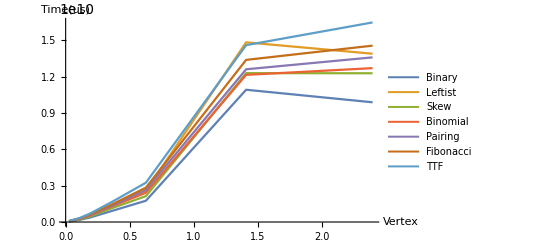

```mathematica
names = {"Binary","Leftist","Skew","Binomial","Pairing","Fibonacci","TTF"};
plots = ListLinePlot[Array[Legended[mat[[#]],names[[#]]]&,7],PlotStyle->Thickness[0.004],AxesLabel->{"Vertex","Time(us)"}]
```